# Практикум №2. Моделирование Гамма-функции

Выполнила студентка ММФ БГУ
КМ, 1 к, 5 гр. Шклярик В.С.
  16 сентября 2021

### Пункт 3

```mathematica
ClearAll[Γ];
Γ[x_/;x<0]:=Γ[x+1]/x
Γ[x_/;1<x]:=(x-1) Γ[x-1];
```

```mathematica
Γ/@{0.2,1,7.6,-0.3,0}
```

{Γ[0.2],Γ[1],1527.7 Γ[0.6],-3.33333 Γ[0.7],Γ[0]}

```mathematica
Γ[-0.9]//Trace
```

{Γ[-0.9],{-0.9<0,True},-Γ[-0.9+1]/0.9,{{-0.9+1,0.1},Γ[0.1],{0.1<0,False},{1<0.1,False},Γ[0.1]},{-1/0.9,-1.11111},Γ[0.1] (-1.11111),-1.11111 Γ[0.1]}

Trace показывает основные шаги вычисления.

```mathematica
DownValues[Γ]
```

{HoldPattern[Γ[x_/;x<0]]:>Γ[x+1]/x,HoldPattern[Γ[x_/;1<x]]:>(x-1) Γ[x-1]}

DownValues показывает правила преобразования, по которым работает функция Γ

### Пункт 4

```mathematica
Γ[x_/;0<x<0.5]:=π/(Sin[π*x]*Γ[1-x])
```

```mathematica
Γ/@{0.2,1,7.6,-0.3,0}
```

{5.3448/Γ[0.8],Γ[1],1527.7 Γ[0.6],-3.33333 Γ[0.7],Γ[0]}

В первом случае функция Γ
Во втором случае

```mathematica
Γ[0.5]
```

Γ[0.5]

```mathematica
Γ[-0.9]
```

```mathematica
DownValues[Γ]
```

{HoldPattern[Γ[x_/;x<0]]:>Γ[x+1]/x,HoldPattern[Γ[x_/;1<x]]:>(x-1) Γ[x-1],HoldPattern[Γ[x_/;0<x<0.5]]:>π/(Sin[π x] Γ[1-x])}

Появились новые правила преобразования, по которым работает функция Γ (формула 5)

### Пункт 5

```mathematica
𝒩=10;
Table[1/2+n/(2𝒩),{n,0,𝒩}]
GammaData=Table[{#,Gamma[#]}&[0.5+0.5*n/𝒩],{n,0,𝒩}]
```

{1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1}

{{0.5,1.77245},{0.55,1.61612},{0.6,1.48919},{0.65,1.3848},{0.7,1.29806},{0.75,1.22542},{0.8,1.16423},{0.85,1.11248},{0.9,1.06863},{0.95,1.03145},{1.,1.}}

```mathematica
TableForm[MapIndexed[{First@#2,#1⟦1⟧,#1⟦2⟧}&,GammaData]]
```

1 | 0.5 | 1.77245
2 | 0.55 | 1.61612
3 | 0.6 | 1.48919
4 | 0.65 | 1.3848
5 | 0.7 | 1.29806
6 | 0.75 | 1.22542
7 | 0.8 | 1.16423
8 | 0.85 | 1.11248
9 | 0.9 | 1.06863
10 | 0.95 | 1.03145
11 | 1. | 1.

```mathematica
DownValues[Γ]
```

{HoldPattern[Γ[x_/;x<0]]:>Γ[x+1]/x,HoldPattern[Γ[x_/;1<x]]:>(x-1) Γ[x-1],HoldPattern[Γ[x_/;0<x<0.5]]:>π/(Sin[π x] Γ[1-x])}

```mathematica
Γ[#]&=MapIndexed[{#1⟦2⟧}&,GammaData]
```

Set::write: Tag Function in Γ[#1]& is Protected.

{{1.77245},{1.61612},{1.48919},{1.3848},{1.29806},{1.22542},{1.16423},{1.11248},{1.06863},{1.03145},{1.}}

```mathematica
Γ[0.55]
```

1.61612

### Пункт 6

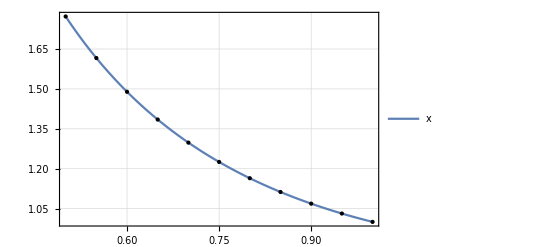

```mathematica
Plot[Gamma[x],{x,1/2,1},PlotTheme->"Detailed",Epilog->{PointSize@Large,Point@GammaData}]
```

### Пункт 7,8

```mathematica
Solve[(Yright-Yleft)/(Xright-Xleft)==(y-Yleft)/(x-Xleft),y]%⟦1,1,2⟧
```

{} {{y→(x Yleft-Xright Yleft-x Yright+Xleft Yright)/(Xleft-Xright)}}

```mathematica
x=0.5321
```

```mathematica
{Xleft,Yleft}=GammaData⟦1⟧
```

{0.5,1.77245}

```mathematica
{Xright,Yright}=GammaData⟦2⟧
```

{0.55,1.61612}

```mathematica
x=0.5321
Solve[(Yright-Yleft)/(Xright-Xleft)==(y-Yleft)/(x-Xleft),y]
%⟦1,1,2⟧
```

0.5321

{{y→1.67209}}

1.67209

### Пункт 9,10,11

```mathematica
Γ[x_/;x<0]:=Γ[x+1]/x
Γ[x_/;1<x]:=(x-1) Γ[x-1]
Γ[x_/;0<x<0.5]:=π/(Sin[π*x]*Γ[1-x])
Γ[#]&=MapIndexed[{#1⟦2⟧}&,GammaData]

Solve[(Yright-Yleft)/(Xright-Xleft)==(y-Yleft)/(x-Xleft),y]%⟦1,1,2⟧
Γ[0]=∞;
```

```mathematica
DownValues[Γ]
```

{HoldPattern[Γ[0.5]]:>1.77245,HoldPattern[Γ[0.5321]]:>(Gamma[x]&)/@{{{0.5},{0.55},{0.6},{0.65},{0.7},{0.75},{0.8},{0.85},{0.9},{0.95},{1.}}},HoldPattern[Γ[0.55]]:>1.61612,HoldPattern[Γ[0.6]]:>1.48919,HoldPattern[Γ[0.65]]:>1.3848,HoldPattern[Γ[0.7]]:>1.29806,HoldPattern[Γ[0.75]]:>1.22542,HoldPattern[Γ[0.8]]:>1.16423,HoldPattern[Γ[0.85]]:>1.11248,HoldPattern[Γ[0.9]]:>1.06863,HoldPattern[Γ[0.95]]:>1.03145,HoldPattern[Γ[1]]:>1,HoldPattern[Γ[#1]]:>{{{1.77245},{1.61612},{1.48919},{1.3848},{1.29806},{1.22542},{1.16423},{1.11248},{1.06863},{1.03145},{1.}}},HoldPattern[Γ[x_/;x<0]]:>Γ[x+1]/x,HoldPattern[Γ[x_/;1<x]]:>(x-1) Γ[x-1],HoldPattern[Γ[x_/;0<x<0.5]]:>π/(Sin[π x] Γ[1-x]),HoldPattern[Γ[x_]]:>{{{1.77245},{1.61612},{1.48919},{1.3848},{1.29806},{1.22542},{1.16423},{1.11248},{1.06863},{1.03145},{1.}}}}

```mathematica
Γ[1.55]
```

0.888868